# reddit api

#### previous

```mathematica
json=Import["http://api.reddit.com/?raw_json=1","RawJSON"];
```

```mathematica
json
```

```mathematica
json//Keys
```

{kind,data}

```mathematica
json["kind"]
```

Listing

```mathematica
json["data"]//Keys
```

{modhash,children,after,before}

```mathematica
json["data","modhash"]
```

```mathematica
json["data","children"]//Head
```

List

```mathematica
json[["data","children",All,"data"]][[1]]//Keys
```

{domain,banned_by,media_embed,subreddit,selftext_html,selftext,likes,suggested_sort,user_reports,secure_media,link_flair_text,id,from_kind,gilded,archived,clicked,report_reasons,author,media,score,approved_by,over_18,hidden,preview,num_comments,thumbnail,subreddit_id,hide_score,edited,link_flair_css_class,author_flair_css_class,downs,secure_media_embed,saved,removal_reason,post_hint,stickied,from,is_self,from_id,permalink,name,created,url,author_flair_text,quarantine,title,created_utc,distinguished,mod_reports,visited,num_reports,ups}

```mathematica
json[["data","children",All,"data","num_comments"]]
```

{2060,73,1133,405,769,93,256,836,87,765,215,3684,296,179,85,702,26,649,74,51,1697,284,193,219,129}

```mathematica
json[["data","children",All,"data","thumbnail"]]
```

```mathematica
Column[thumbnails=json[["data","children",All,"data","thumbnail"]]]
```

http://b.thumbs.redditmedia.com/_V01mRzuq_9O0l7pDaFclnnujQDOoNgWlR7aNj4jd9E.jpg
http://b.thumbs.redditmedia.com/URq5vfDSteJm1gpM3gJ0I2IdmC0SF6iFVa7so85clbc.jpg
http://b.thumbs.redditmedia.com/UVZv_g6UDzfaIRGG0FmCQNXKUb9WHcC9WfcQ7NeM-xs.jpg
http://b.thumbs.redditmedia.com/QSlklRVQhVhep2aCiamVeBClecBowazvV1jFnElv6AE.jpg

http://b.thumbs.redditmedia.com/IwpK7sCXS_CH0wX2wDcEtjtJTr0N7azU8Y7Pg3m38IE.jpg
http://a.thumbs.redditmedia.com/0SWVydmjdcEQVfd_vXHe_s_nrV3WqKeZSxvyAMtEE48.jpg
http://b.thumbs.redditmedia.com/jFAVICD4aqnBF5c1wkyMCGOcgdUw6GTQXHnimcfZRyQ.jpg
http://b.thumbs.redditmedia.com/vOVqcvGu6Wq5MUmrEJ8iALmSyoDmLP9AFjfDtbBoXDE.jpg

http://b.thumbs.redditmedia.com/UogYEERu10p42cjtQzI1COwiHNOaHttMbEpu-gHsDWA.jpg

http://b.thumbs.redditmedia.com/7BtCCwnGL0TYU6fpiQImMFuCXu1sHV5OdGl7q_Er74U.jpg
http://b.thumbs.redditmedia.com/RDlqoQkqPCnQpWLbgXmkAaGQ-xTp5TqYP9g-Gczs2QM.jpg
http://a.thumbs.redditmedia.com/hiYyQrkUUNBiMlXeGmnN69ywYGt8H0B2fFXbTuL0_Y4.jpg

http://a.thumbs.redditmedia.com/2tG5X5BFIanVgz8Nfb2EFAwxB_taL161ptarBUeJX34.jpg
http://b.thumbs.redditmedia.com/xfNLNsqWj8rcA_Pf3d12S7LPw-cceiHClTFQKTQGw_I.jpg
http://b.thumbs.redditmedia.com/sDTjfMjbk0KCHTKtLd65Gwb58Vpg4qoeYJ6X9t03pwY.jpg
http://b.thumbs.redditmedia.com/2zgMsUf7biWERcXhpYwfOOCVIII8aQ4r8VNEi9DuM0w.jpg
nsfw
self

http://b.thumbs.redditmedia.com/n3d536XIP64eogrjFktRDuIkoNe7KWE94-76PCquBNE.jpg

```mathematica
topImages=DeleteCases[If[StringMatchQ[#,"http"~~___],Import[#]]&/@thumbnails,Null]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[{#,ImageIdentify[#]}&,topImages]//Grid
```

-Graphics- | dinner table
-Graphics- | person
-Graphics- | bacteria
-Graphics- | hurdle
-Graphics- | person
-Graphics- | mount
-Graphics- | telescopic sight
-Graphics- | whale
-Graphics- | person
-Graphics- | path
-Graphics- | mug
-Graphics- | domestic cat
-Graphics- | painting
-Graphics- | person
-Graphics- | person
-Graphics- | person
-Graphics- | dialog box

```mathematica
json[["data","children",All,"data","domain"]]
```

{fortune.com,i.imgur.com,thelatestnews.com,i.imgur.com,dailymail.co.uk,i.imgur.com,imgur.com,vimeo.com,self.tifu,self.AskReddit,i.imgur.com,i.imgur.com,latimes.com,i.imgur.com,i.imgur.com,i.imgur.com,sportpicss.com,i.imgur.com,imgur.com,i.imgur.com,self.IAmA,self.Showerthoughts,self.Jokes,youtube.com,samuelwbennett.com}

```mathematica
json[["data","children",All,"data","subreddit"]]
```

{todayilearned,pics,science,funny,worldnews,aww,mildlyinteresting,videos,tifu,AskReddit,space,EarthPorn,news,OldSchoolCool,gifs,photoshopbattles,sports,gaming,food,Art,IAmA,Showerthoughts,Jokes,movies,dataisbeautiful}

```mathematica
frontpage=json[["data","children",All,"data",{"score","num_comments","author","subreddit","title","url","thumbnail"}]]//Dataset
```

score | num_comments | author | subreddit | title | url | thumbnail
6515 | 1687 | TheCannon | todayilearned | TIL after a Pittsburgh Restaurant Owner did away with tipping, paid employees a base salary of at least $35k/year (plus bonuses), gave them health care from date of hire, 500 shares in the business and a paid vacation, the restaurant tripled its profits in 2 months. | http://fortune.com/2015/06/11/bar-marco-no-tipping-policy/ | http://b.thumbs.redditmedia.com/_V01mRzuq_9O0l7pDaFclnnujQDOoNgWlR7aNj4jd9E.jpg
5412 | 354 | CANT_TRUST_HILLARY | pics | Seen at the airport in Tel Aviv, Israel | http://i.imgur.com/ZhvlFlq.jpg | http://b.thumbs.redditmedia.com/QSlklRVQhVhep2aCiamVeBClecBowazvV1jFnElv6AE.jpg
4526 | 962 | elbartos29 | science | New study confirms that smoking causes emphysema due to incomplete combustion of insoluble nanoparticulate of carbon and the longer you smoke the worse it gets | http://www.thelatestnews.com/emphysema-linked-to-carbon-nanoparticles/ | http://b.thumbs.redditmedia.com/UVZv_g6UDzfaIRGG0FmCQNXKUb9WHcC9WfcQ7NeM-xs.jpg
4240 | 718 | CopyRasta | funny | Society in 2015 be like | http://i.imgur.com/ysWL9hP.jpg | http://a.thumbs.redditmedia.com/oVYMU82h9MgTQNtpm-XxVyjIboJ77YXt12JZz_HTRY4.jpg
4889 | 690 | santaschesthairs | worldnews | 'Nightmares, bed-wetting and behavioural problems': Australian Doctors refuse to discharge sick children back to detention centres - despite government's threat of two years in jail for speaking out on the issue | http://www.dailymail.co.uk/news/article-3267877/Nightmares-bed-wetting-behavioural-problems-Doctors-refuse-discharge-sick-children-detention-centres-despite-government-s-threat-two-years-jail-speaking-issue.html | 
3087 | 46 | mattythedog | aww | Sleepy puppies | http://i.imgur.com/WQZsgRJ.gifv | http://b.thumbs.redditmedia.com/URq5vfDSteJm1gpM3gJ0I2IdmC0SF6iFVa7so85clbc.jpg
4220 | 219 | michaelsiemsen | mildlyinteresting | My plane's jet heat made a tilt-shift effect on San Francisco. | http://imgur.com/P2r5N47 | http://a.thumbs.redditmedia.com/0SWVydmjdcEQVfd_vXHe_s_nrV3WqKeZSxvyAMtEE48.jpg
3713 | 673 | zxzxzx207 | videos | AK firing | https://vimeo.com/141863331 | http://b.thumbs.redditmedia.com/jFAVICD4aqnBF5c1wkyMCGOcgdUw6GTQXHnimcfZRyQ.jpg
1876 | 549 | jihalliday | tifu | TIFU by not paying attention to the kid I was babysitting [NSFL..?] | https://www.reddit.com/r/tifu/comments/3obt48/tifu_by_not_paying_attention_to_the_kid_i_was/ | 
2866 | 2967 | crumbbelly | AskReddit | Reddit, what makes you instantly like someone upon meeting them? | https://www.reddit.com/r/AskReddit/comments/3obi7b/reddit_what_makes_you_instantly_like_someone_upon/ | 
1569 | 51 | inefekt | space | This is a 42 shot, 110MP, 'horizon to horizon' image of the Milky Way I took from outback Western Australia recently. | http://i.imgur.com/PgYKaSd.jpg | http://b.thumbs.redditmedia.com/vOVqcvGu6Wq5MUmrEJ8iALmSyoDmLP9AFjfDtbBoXDE.jpg
1331 | 27 | krajacic | EarthPorn | Grand Teton National Park, U.S. [2048x1054] © Dream Afar | http://i.imgur.com/7XjDNIa.jpg | http://b.thumbs.redditmedia.com/ip3T2UdiYxQnC_xLSAZWAGvCAavmb6iXB59E5ncEViY.jpg
3354 | 591 | Unwanted_Commentary | news | Rand Paul's Filibuster on the Patriot Act has been going on for 143 days. | http://www.latimes.com/rand-paul-filibusters-patriot-act-htmlstory.html | 
1300 | 124 | Meunderwears | OldSchoolCool | Stewardess for United Airlines in 1970. | https://i.imgur.com/tLwjC3J.png | http://b.thumbs.redditmedia.com/UogYEERu10p42cjtQzI1COwiHNOaHttMbEpu-gHsDWA.jpg
5474 | 620 | namraka | gifs | "Did you close the fridge door?" | http://i.imgur.com/kaFzwUY.gifv | http://b.thumbs.redditmedia.com/xfNLNsqWj8rcA_Pf3d12S7LPw-cceiHClTFQKTQGw_I.jpg
1471 | 70 | SpyDBM | photoshopbattles | PsBattle: Those cats yawning | http://i.imgur.com/JYrFPHk.jpg | http://a.thumbs.redditmedia.com/hiYyQrkUUNBiMlXeGmnN69ywYGt8H0B2fFXbTuL0_Y4.jpg
⋮_9 |  |  |  |  |  | 
2 levels | 25rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
Dataset`$ElisionThreshold=2^20;
```

```mathematica
frontpage[All,<|
"score"->#score,
"num_comments"->#"num_comments",
"thumbnail"->If[StringMatchQ[#thumbnail,"http"~~___],Button[Image[Import[#thumbnail],ImageSize->Tiny],#url],"—"],
"author"->Hyperlink[#author,"https://www.reddit.com/user/"<>#author],
"subreddit"->Hyperlink[#subreddit,"https://www.reddit.com/r/"<>#subreddit],
"title"->Hyperlink[#title,#url]
|>&]
```

score | num_comments | thumbnail | author | subreddit | title
6515 | 1687 | -Graphics- |  |  | 
5412 | 354 | -Graphics- |  |  | 
4526 | 962 | -Graphics- |  |  | 
4240 | 718 | -Graphics- |  |  | 
4889 | 690 | — |  |  | 
3087 | 46 | -Graphics- |  |  | 
4220 | 219 | -Graphics- |  |  | 
3713 | 673 | -Graphics- |  |  | 
1876 | 549 | — |  |  | 
2866 | 2967 | — |  |  | 
1569 | 51 | -Graphics- |  |  | 
1331 | 27 | -Graphics- |  |  | 
3354 | 591 | — |  |  | 
1300 | 124 | -Graphics- |  |  | 
5474 | 620 | -Graphics- |  |  | 
1471 | 70 | -Graphics- |  |  | 
1032 | 221 | -Graphics- |  |  | 
4950 | 336 | -Graphics- |  |  | 
737 | 93 | -Graphics- |  |  | 
760 | 15 | -Graphics- |  |  | 
2478 | 1601 | — |  |  | 
4067 | 263 | — |  |  | 
3175 | 123 | — |  |  | 
4649 | 1228 | -Graphics- |  |  | 
430 | 175 | -Graphics- |  |  | 
2 levels | 25rows |  |  |  |  | Dataset[{__Association}]

#### now

```mathematica
Dataset`$ElisionThreshold=10^10;
```

```mathematica
json=Import["http://api.reddit.com/?raw_json=1","RawJSON"];
```

```mathematica
json//Keys
```

{kind,data}

```mathematica
json["kind"]
```

Listing

```mathematica
json["data"]//Keys
```

{modhash,children,after,before}

```mathematica
(urls=json[["data","children",All,"data","permalink"]])//Column
```

/r/todayilearned/comments/3obs1z/til_after_a_pittsburgh_restaurant_owner_did_away/
/r/pics/comments/3obojx/seen_at_the_airport_in_tel_aviv_israel/
/r/science/comments/3obphj/new_study_confirms_that_smoking_causes_emphysema/
/r/aww/comments/3obth9/sleepy_puppies/
/r/worldnews/comments/3obj2r/nightmares_bedwetting_and_behavioural_problems/
/r/funny/comments/3oboqn/society_in_2015_be_like/
/r/mildlyinteresting/comments/3obkmp/my_planes_jet_heat_made_a_tiltshift_effect_on_san/
/r/videos/comments/3oblem/ak_firing/
/r/tifu/comments/3obt48/tifu_by_not_paying_attention_to_the_kid_i_was/
/r/space/comments/3obsvo/this_is_a_42_shot_110mp_horizon_to_horizon_image/
/r/AskReddit/comments/3obi7b/reddit_what_makes_you_instantly_like_someone_upon/
/r/OldSchoolCool/comments/3obv7l/stewardess_for_united_airlines_in_1970/
/r/sports/comments/3obxi3/when_men_are_forced_to_go_to_the_mall_on_a/
/r/news/comments/3ob8y1/rand_pauls_filibuster_on_the_patriot_act_has_been/
/r/photoshopbattles/comments/3obof8/psbattle_those_cats_yawning/
/r/food/comments/3oc0a7/nutella_donut_milkshake/
/r/gifs/comments/3oav7v/did_you_close_the_fridge_door/
/r/Art/comments/3obxj6/regal_phoenix_by_katy_lipscomb_colour_pencils_and/
/r/gaming/comments/3oaorm/get_out_of_my_way/
/r/IAmA/comments/3ob0hs/ama_request_the_2_girls_1_cup_actresses/
/r/Showerthoughts/comments/3oahxy/one_of_the_lesser_known_advantages_of_owning_a/
/r/creepy/comments/3obltt/list_of_things_that_are_actually_creepy_mostly/
/r/Jokes/comments/3oajo2/damn_girl_are_you_rjokes/
/r/dataisbeautiful/comments/3obr2o/a_comparison_of_professional_athlete_arrest_rates/
/r/askscience/comments/3obzfm/if_we_can_produce_zerocalorie_drinks_easily_why/

```mathematica
listing=Import["http://api.reddit.com"<>urls[[1]]<>"?raw_json=1","JSON"];
```

```mathematica
comments=Cases[listing,HoldPattern["body"->body_]:>body,Infinity]
```

{I worked in the restaurant industry for 25 years. I was a manager for 15 years. We had a 10% spillage/comp for the night for bartenders and wait staff each night at a few places I worked. These were fine dining joints where comping a guest's appetizer, dessert, or a couple drinks was common place. One place I bartended at had a mandatory 15% spillage each night. Rich people expect free shit. You're right, it keeps employees from stealing to make better tips, too.,A lot of well run restaurants have weekly allowable comps for servers and bartenders to use to encourage repeat business, send out a free app or buy a drink for a new guest who you think will return or a regular. Places without allowable comps likely have all sorts of "spillage" due to people sending out free drinks on the sly.,He'd tell me to fuck myself and my whole family.,Hey Cookie, there was a mistake on that plate. Can you make me another?,So at my restaurant the waiters get a free meal worth $15 or less if you work a double and 50% off for a normal shift. However, we use iPads to punch in orders at the table and they are super strict about the system so I wouldn't be able to tell the chef, "Hey make me this and I'll pay for it later." If it's not in the computer system it's not getting made (save certain situations like re-making a plate because of a mistake or something.) ,I've heard some restaurants allow staff a sort of ration of their wares sort of like how it's common to allow fast food workers a meal or so depending upon shift length and all that. So that'd be like giving out your rations of drinks or food for the day rather than a direct charge-back.,That's exactly it. The most expensive thing in a restaurant is an empty seat,I I don't buy everyone stuff. First time couples, regulars. If it gets them back in the door to see me again, I'm making money ,Really? Doesn't that destroy your pay?,That rustles my jimmies so much and I've never worked a tipping job. It just seems so disingenuous, they literally get someones hopes up and them dash them with some theological bait and switch and it's somehow supposed to encourage people to seek out your philosophy? That is a laughable introduction at best and a bitter one at worst. What other fake carrots is your religion going to dangle in front of me? 

Ugh, if you don't want to tip, then don't tip. And if you want to proselytize then just leave a regular pamphlet instead of counterfeit money. 


Swear there are 3 kinds of people in the world; dicks, pussies, and assholes. Those people clearly fall in the asshole category. ,That's messed up. I'd love to replace their paycheck with useless paper advice and see how they like it. I bet they felt all good afterwards, like they had done a good deed. Religion can make people do a lot of good, but it can also make them do some pretty messed up things...,No, I've never received a real one in the cases where someone leaves a fake-out. Sometimes they leave a dollar or two inside a tract, that's totally different in my opinion.,Does the Sunday crowd also leave a real tip in with the fake tip? Or is the fake tip the only thing they leave? If the latter, that's so douche-canoe-y,Wow that's bs. I'd be pissed at the ruse. Your God requires deception and false hope to recruit? No thanks.

Seen the movie about waiters at a nice restaurant? Not waiting the one with the boxer as owner. 

Guy comes and orders coffee camps on table reading a book. Waiters complain dump table on new guy. Turns out it's his last night on earth. Gives like a 10k tip.,Last Thanksgiving, a tiny old lady came into my restaurant and sat down to eat a turkey dinner. This was the first year she had come in alone - her husband had passed away a few months before. 

So a couple coworkers got together and contributed to buy the meal for her. Wouldn't anyone? Hell, other customers will sometimes buy the meals of strangers at other tables. What do you mean, 'why'? 

Serving can be a very personal profession. You see the same people and have a little personal time with them as you get to know them, and sometimes people will come in who haven't got any money and are asking for whatever we can give them. Most of us have been down on our luck, if we aren't at that moment, and so we do what we can to help people sometimes. The money isn't recouped and that's kind of the point. 

edit: I'll take this moment to point out that the Sunday crowd will still leave us [fake tips with tracts](http://i.imgur.com/rnujsRt.jpg) on them to save our souls, though,Not OP, but I worked at a beach spot in Panama City and made loads of money waiting tables.

There were basically 2 reasons.

1) Girl was really hot at the table.  Thought there was a chance.  Pulled out the stops.

2) I felt like I fucked up the tables order or otherwise did shitty service to the table.  I made $300 a shift some nights, a 7 dollar drink wasn't going to break me.,Assuming you aren't joking...

Why?

Do you recoup the money spent?,As a server, I buy my tables things with my own money and say it's on me... Because it is,nah... was there with husband and 3 male friends. It is not like we were 5 college girls. We are all old people.
,damn, you must be attractive,There is a bar we go every Friday, and the fairly new waiter just gave us a lot of drinks for free.  I left wondering if the manager was aware of it, because it was almost 1/3 of the bill left out. I pointed out to him and he told me " it is one me" when in fact, probably " it is on the restaurant".,I reaaally like the profit sharing. If I work as a line cook making lets say 11 an hour, I work my ass off in the weeds all weekend and sacrifice my free time to come in early and prep and be at the restaurant all day and night 6 days a week then Ill enjoy it more knowing my rushing around and making sure every dish is done right will ultimately be to my betterment.,I'd actually assume a lot of the booze costs went to the staff helping themselves to a drink here and there, in addition to what you say about overpours, etc. When your pay is directly tied to profit margin, etc., you tend to more do what's right for the business, because it is also right for you.,Overpouring is definitely a thing.  If I'm going to become a regular at a bar, I usually tip insanely well a few times (and still well, but not insanely well after that).  I get free shit and and really strong drinks all the time.,Your important takeaway is that what they did, and what other businesses can do, is more efficiently structure their operations and capital expenditures, and pass the difference on to the employees.  This is precisely what my friend does with his business.  He doesn't take a huge CEO salary.  The stability of his income depends on the stability of the business
The challenge is how to incentivize non entrepreneur managers to think like this. ,Most likely, wages have gone up offset by overhead which has gone down. 

The article just touches briefly upon reduced portion sizes, so that's a part of it. It also talks of a more efficient bar inventory which is kind of vague. having worked as a server and bartender and having a restaurant general manager for a brother, it is not uncommon to see servers and tenders to overpour and to otherwise give away restaurant services, hoping for a bigger tip. I'm willing to bet the booze costs have gone down even though sales have remained constant or gone up.

The no tip/profit sharing model is an interesting one for restaurants, And one I think will continue to grow in popularity, at least at the mid-to-upper scale restaurants.,14$ without tip don't forget.,$14 including tip is typical for a specialty burger just at your average bar around here.,If the people in r/personalfinance hear you they might have a brain aneurism. ,Nah, Redditors are just cheap. $14 is typical for a specialty burger at any upscale (meaning non-chain & good quality) place.,I was going to point this out. In paces that are doing well- Seattle, Denver, Minneapolis, New York, etc. - $14 for a good burger, fries, and a side is pretty darn reasonable.

I think a lot of these posts complaining have lower costs of living.,Depends where.  If you want a burger in a restaurant in the greater Seattle area in a place of quality with good ambiance you'll pay $14-15 for a burger.

,$14 is £9.13 today and in England you'd absolutely expect to pay that give or take 50p for a burger at a restaurant. It just surprised me that in America that's considered very expensive I suppose.,Don't forget that you're going to a place where the waiters, waitresses, busboys, cooks and dishwashers all have a stake in the success of the business. Owning 500 shares and watching it grow, knowing you can get more for good work, and most important, knowing that you control the fate of those shares, is powerful. And not nearly seen enough in America today. 

This guy should run for President. Because this is what a business is supposed to look like. 

,Thanks for this. People below are bickering about $14 for a burger being pricey. But they're proving my point ultimately.  This place is successful because they have a large enough clientele that goes "$14 for a burger isn't bad!".

When about $10 is more standard for a deli or diner, and the "fancy" fast food places top out at about $6.,It is quite an expensive place in general. I did a wine pairing special menu there for Valentines Day last years, while it was really good, it was also very pricey. 

The staff is very good, attentive and friendly as well. Not to mention the owner personally corresponded with me in order to get the reservation solidified. He followed up multiple times via phone and email just to make sure everything was on track.,Is it a cat... in a hat? *no... its a tortoise, in a shell*,this is a tortoise,What kind of McDonald's is this?,Is it expensive if you consider no 20% tip on top of this? This is at the higher end, but now it's equivalent of a $11-12 burger.,Yeah, but Memphis. 

[It's is one of the least expensive cities in the US.](https://www.zumper.com/blog/2015/09/zumper-national-rent-report-september-2015/),No chance. Bacon Cheeseburger, large fries and reg drink is CAN$15.86 in Canada, it's $32.25 in the UK.,The fries are your problem. The "regular" fries they serve are family sized and priced accordingly.,$ =! £,uhhh... 5 guys is about just as expensive in Canada. I remember going and a burger and fries was about $15.,UK pricing is ludicrous on everything. I honestly don't understand how you guys get by as your salaries are about the same as ours in Canada but prices are more or less double. ,"5 Guys" is a restaurant, BTW.,Just for a comparison. A 5 guys meal over here with a drink etc you are looking at at least £10.00 

(Large chips and a drink with a bacon cheeseburger is around £15.),Crazy. In Memphis you can get in and out of a burger joint (not fast food and real beef) for roughly $6-8. With beer and fries it might push you to $12.,Maybe if your cost of living is high. I can get a burger where I live for eight dollars that includes fries. Half pound.,a very decent point.  You can basically cut all their prices by 20% to compare them to what you would pay somewhere else.  ,Does that include fries or a side?

And is this a plain burger, or a burger with cheese, bacon, fried egg, etc?

Red Robin is a nationwide sit down chain. Their cheeseburger is $9 and includes fries. At a lot of sit down chains, that is about par. If you start throwing on bacon or ordering specialty burgers, you might get up to $14 with fries.

You can go to McDonalds/Burger King, etc. and get some sort of combo for $6.

If this place is charging $14 for a burger without fries or extras, then that is a bit much. If that is a high-end burger with fries, it isn't completely out of line.,But even 10-12 becomes 12-14 after tip ,Had a $24 burger once at a Hilton in Washington DC. My lord I would pay again. It was worth every penny. ,Burgers are good, but I find only a marginal difference between  $10 burger and anything above that.,I've eaten a lot of burgers. $14 is on the high of average, they're usually $10-12, and at some bars and cheaper places, $8-10. For my money, $18 is high end for a burger, and fuck me in the ass if I'm paying $20+ for one unless it's In-N-Out. As a Floridian, I would pay $20 for In-N-Out.,Varies by location though. In a major metropolitan area, sure. Rural areas not so much.,It really isn't outside of diners. Anywhere I go that's a sit down place it'll be $12-$16 for a burger, fries, etc.,$14 is expensive for a burger in the U.S.

edit: [Average burger price is apparently in the $9 range in NYC, the most expensive major city in America to buy a burger.](http://www.eater.com/2015/4/17/8447769/the-average-price-of-a-burger-across-american-cities) So yes, your $14 burger you think is cheap or average is actually expensive. ,It's fine for a major city burger (NYC, SF).

It might be fine with GBP prices/normal food costs, or in London.

It is a bit on the high end for most places in the USA with USD pricing, like Pittsburgh. Not crazy, but it's not "very reasonable". It had better be a good burger at a fancy place, or the $14 better be part of a larger platter (two sides).,UK food prices are way higher than in the US. When I went there the pound was worth two dollars and I could have sworn the Burger King we went to when we took a coach to Durham had the same prices as in the US but with a pound sign instead of a dollar sign.,I don't think it's on the high side at all. I think $14 (£9) is very reasonable?,Right? $14 might be a little on the high side, but that's about what you pay for Ruby Tuesday's most expensive Prime beef burger.,In the UK. It's more expensive than a McDonald's burger, but it would be on the cheap side for a burger served in a non-fast food restaurant. Although that price would include chips/fries.,It's expensive for a burger that you would get at say Denny's or IHOP, but for a specialty burger, depending on what's in it, it's not unreasonable. ,Philadelphia here, out last night had a burger at Village Whiskey....a nice but casual spot.....$18.50, on the upper end here but not an outlier....... and it didn't really seem so bad next to my liquor total $.,I paid £15 on Friday night. I thought it was worth every penny. 
(No I don't live in London). ,Food in the United States is cheaper overall, though. That's what the farm subsidies are supposed to do.,The UK. Here £9 is pretty much standard if it isn't fast food.,Standard price for good quality burgers, at least in the upper scale pubs,a $14 hamburger is completely normal anywhere in Canada that you would sit down at.  Maybe a *tiny* bit on the high side. I mean that will come with fries and a drink of course,Where isn't that expensive?,Is $14 for a burger expensive?,Everything about this restaurant points to success in it's clientele base, not financial practices. 

 The food prices and items listed suggest they bring in a crowd that would love whatever the hell an espresso burger is and happily pay $14 for one. 

Edit:  this is turning into a weird argument about burger price. My point was that not every restaurant has clientele that will pay that much.  Example: my favorite place for pupusas charges $1.50-2.50 per.  Go into the city and food trucks charge 3x because the clientele sees it as reasonable.  Meanwhile if my local place suddenly charged 3x for everything they'd likely close shop within a year.,There's a lot more that doesn't make sense in the article. Operations costs plummeted based on what, it doesn't say expect for employees are paid more. The article seems to indicate, the retooled menu means smaller portions at higher prices...well, duh that has nothing to do with playing employees more. Also, higher quality ingredients cost less?? On what planet? 

What you see here is nothing but 'fashion' and 'trendy'. Revisit this restaurant a year from now and you'll see less staff due to layoffs, another retooled menu and higher costs passed to the consumer just to keep the doors open.,but if they're salaried now, I'm assuming they get health care and a retirement plan. which can be invaluable, and worth far more than $5K per year (in the long run). ,He's also offering a full benefits package too though. $35K+benefits is equivalent to $40-$50K without benefits for most people.,The owner did an interview on local TV here in Pittsburgh recently and said that the average salary he expects to pay out is $51k after bonuses. Since the employees have a share of the business and they have twice a month business meetings to go over everything, their costs such as linens and water/electric/gas and food waste have all gone down. The employees are much more mindful of the overhead when they get a piece back.,I think a stable lifestyle out trumps higher pay at an unreliable rate. Restaurant servers often have bad lifestyles because of their boom or bust paycheques. Some weeks they make a lot of money and therefore blow it all on frivolous things, while other weeks they are barely scraping by. A steady paycheque fosters better budgeting habits, and I would argue a better lifestyle.,Exactly.  What happened here is that owner figured out he could charge a ~20% premium on his prices if he implemented a no tipping policy, in addition to getting free press for the gimick.  $35k is a pretty low wage for a server in a restaurant with $15 burgers.  That's barely $100 per shift for a full time server, which is actually pretty low for a fancy restaurant, compared to collecting tips.  Hell, I used to clear $100/shift just in bar tip-out at a similar place.  An experienced server at a nice restaurant can easily clear $40k-50k or more.,This is basically how rappers survive,http://images.luvimages.com/luvphotos/h/homer_simpson_gif-761.jpg,This is startling.,Totally unexpected drama in the comments, and an appalling story. Good luck mate. ,Whoa. This shit is personal. Did not expect that. ,This just got good.,I blame reddit for the fact that my first thought is that this is probably the same person on two different accounts doing a little theater for my own amusement.

That said, I don't even care... Damn son.,At first I thought you were a psycho, but after doing some reading into the person you're replying to, man, is she a fucking cunt.,Oh I'm sure you're right.

  But she literally says, "Our parents abandoned us when we were quite young so I was made to care for us both..." in my second link.  She also says says her parents paid for her education, her parents abandoned her, and her dad took her to watch a fight, a few months apart.  ,she literally says the money is worth more than the relationship with her day. holy fuck. I am surprised, but I shouldn't be:

>[My first thought when I heard the news was not "Oh god. is he ok?" It was more like "Does that mean i still have to pay off my debt?"](https://np.reddit.com/r/opiates/comments/3myp45/alright_this_shit_stops_today/) 

they didn't "abandon her." they kicked her out for stealing from them. (which was likely due to her drug habit, although she'll claim it isn't),Don't forget wanting to sue your father because you lost a bet by following his advice :  

https://www.reddit.com/r/legaladvice/comments/34t8pi/my_dad_scammed_me_out_of_5000_should_i_sue_id/

But don't forget, the same parents who paid for your school and that you wanted to sue, abandoned you and did not raise you:

https://www.reddit.com/r/relationships/comments/3gg187/my20f_little_sister_17f_wants_her_ex_boyfriend_to/,I'm pretty sure they are OK with running away, dunno if you realistically expect them to repent and publically admit their failings or if a reddit callout is the only justice left

I love this kinda drama though, brb popcorn,Well fucking A.,Damn son, this Karri seems to be a real fuckhead. Cheers for the persistence mate.,I think this is nonsense, both accounts are fake and they probably just publicly duke it out for fun with these fictional characters. 

 Good work though, very convincing.,>Where I work the higher-ups do this all the time.

yeah but where you work lets you in on the good word of a [career counselor you were blowing](https://www.reddit.com/r/AskReddit/comments/3mvwha/what_is_the_most_fucked_up_family_secret_that_you/cviu7o9?context=3) so that's hardly telling.

you still haven't answered my question from [here](https://www.reddit.com/r/todayilearned/comments/3o3ppx/til_that_despite_the_claim_that_100_of_your/cvttdwv).

how does it feel to screw everyone who worked hard for that job? The ones who didn't get to go to a private school, nor got a career counselor to bang when things got tough?

do you think that maybe, just maybe, you could have done better than getting your 30 dollar an hour job to throw all your money on heroin, get a debt with a drug dealer and cause the death of your boyfriend? (My best friend, if it wasn't already obvious)

do you think you could have done better for [your sister](https://www.reddit.com/r/TwoXChromosomes/comments/3lb3nq/my_abusive_sisters_finally_been_evicted/) (who's now moved on to the needle btw, I know you haven't checked on her, I have been doing that for you) ?

do you think you could have done better than flee the country instead of having to face me or his family? You still won't respond to any messages unless they're posted publicly like this.

all they want is an apology. an apology for causing the death of their kid. 



Why can't you do that? Why do I have to call you out in public?

it's not something i want to do, but you won't acknowledge what you did any other way. (you even went as far as to block everyone from facebook)

it's your choice. PM me or run away from what you did for the third time. i'm not going to harass you, so if you don't respond this time ill leave it be. im sure everyone here would like some kind of explanation or just some kind of effort to show that you recognize what you did.,He has every incentive to mislead. He'll only stand to gain a bunch of publicity from the article, and have everyone think his business is great and profitable. (And if it's profitable, it must be good right?) Where I work the higher-ups do this all the time. Showing how successful you are makes you more successful. (And it even works if you make it up)


Edit: Looking back at it, the article gives the name and location of the place in *literally the first line.*,The reality is that this *can* be good for business, at least for a while, and as long as you're the only one doing it. 

-it gets you good publicity. 

-people will patronize the establishment just to support the concept. 

-you can take advantage of the first two points to screw the customers with smaller portions and lower quality food, because people are eating there to make a point. 

But of course that will all die out over time. There is, of course, nothing stopping him from reverting back to the original pay structure when the do-gooders stop showing up. But I'm sure the first couple of months are great. ,Yeah, the overhead only increasing 1k for an increase in 7k sales, doubling the wage for the whole serving staff (and possibly hostesses and cooks getting a raise) would increase the labor costs so you would have to have seen a huge cut in food cost as a percentage of sales (which should be fairly impossible). I don't believe these numbers at all.,If it is true, it's great. But traditionally restaraunts have very low profit margins, hard to believe they would increase profits by so much without multiplying the price of menu item 5x over. ,If this was true you would think he would stick with the company rather than selling off his shares earlier this month.,I think this is great if true, but the numbers don't seem to stack up. This bit in particular..

>Weekly profits of about $3,000 (after $26,000 in sales) have now climbed to $9,000 (after roughly $33,000 in sales,) he says.

So wages and overheads have gone from 23k to 24k per week? They must have been paid pretty well before this change.
,People talk about what they're paid by the restaurant and not what they earn.

The tipping system exists for a reason. It does get you better service and better servers at nice restaurants. 

At a nice place you can make a LOT of money. An old friend of mine was a server at a fondue restaurant. Avg bill was close to $100 per guest. He worked 3 nights a week sat/sun/one midweek night for 7 hour shifts and made about $2500 per month. ,So, are servers really underpaid then? Reddit loves to talk about how servers are paid horribly but I'd like to know how much servers are paid compared to the kitchen staff.,I worked at a shoddy restaurant with insanely high quality steaks. Seats only 30-40 people but on friday or saturday nights, I walked out with over $300 in tips alone. And thats with splitting it with another server. I worked 6 hours a day 48 hours a month, 2 days a week and was making $1200-$1600 a month. The bill for 2 people was on average $100+ dollars though.   ,Bar I frequent has a few people who rotate from being the on shift manager (no tips), to doing tables, to tending the bar.

One said she makes the least amount as manager at 15/hr with no tips.  Tables she usually makes "a little bit more."  The two nights a week she is at the bar she makes 30/hr on average.

This place isn't a total dive, but it isn't nice either and she brings in an average of about 20/hr or 40k a year.  Granted only 6 of them are on this rotation, the rest just do tables all the time and will make substantially less, but those servers tend to be worse that the ones who spend time at the bar.,so few good weekends and quarter of the rent for that single room is payed.,I have a friend who is a bartender in a high end restaurant in SF and he says on a good weekend night he can pull in over 2,000 in tips.

I can see why everyone working at a high-scale place wouldn't appreciate the no tips.,My wife went from being a bar tender at a fancier place to being a store manager for a large national retail chain, and took a pay cut in doing so.  The benefits are better, and there is opportunity for advancement, but the initial decision was harder than what it should be for moving away from what reddit seems to view as a "an unskilled job for teenagers."  
  
,People get pretty bad pay across all sorts of industries you'd think would compensate better and focusing upon just a single industry erodes away at the reality that almost everyone is getting taken advantage of in the US. I know an accomplished, published professor in the sciences at a prominent US university that says with zero sarcasm "I miss the pay of being a server.",Yup $35k is quite low for a nice place. It's not surprising that skilled servers would not want to take a *de facto* pay cut.,The people who complain about tipping simply have never worked in a restaurant and have absolutely no clue how much servers can make.,I'm good friends with the former head chef who also left the restaurant but for different reasons.,Do you know anyone who worked there, or anything like that?,All I know is that a few months after enacting this policy, most of the FOH staff quit or starting working at the owners' other restaurant, The Livermore. After they announced that The Livermore was also switching to the same no tip policy, the entire FOH staff walked out. The staff found out about the change in policy from an owner's post on Twitter.

Edit: The article below mentions the "near complete turnaround of staff" at their other restaurant, with a few quotes from former FOH staff.

http://www.pittsburghmagazine.com/Best-of-the-Burgh-Blogs/Eat-Street/June-2015/Change-of-Focus-at-Popular-Pittsburgh-Cocktail-Spot/,Neat. So it incentivizes service for more expensive meals. Why risk losing half of $10 over half of $4?

Never considered the trade off since the restaurant I served at was mostly in a set range per diner, and I mainly tended bar.,I'm always a percentage based tipper, but I have a friend that is a per person tipper. He just always throws in $3 per person per meal. Doesn't matter if everyone got $8 cheeseburgers or $30 steaks. He's not annoying with sauces or refills. If he orders alcohol it's a flat $1 per drink.

So for example, he, his wife, and daughter go to dinner. They order $30 worth of food and four beers. He would tip $9 for the food plus $4 for the beers.

If just he and his wife go out and order $60 worth of food, and four beers, he would do $6 for the food plus $4 for the beers. 

When we go out to eat, sometimes he ends up tipping more than me and sometimes he ends up tipping less. His logic is that the waiter spends the same amount of time per person (since a single family is consistent normally) no matter what they eat, so it doesn't make much sense to go on percentage, but on stops at the table.

How do you feel about that process?,You offer a lot of good points, but from the consumer point of view one part of your explanation is off to me:
> restaurants sell an experience, not a product

I disagree.  Restaurants sell a product, wait staff sell an experience.  I pay the restaurant for the food I order; I tip the waiter for the experience I received.,I am a fine dining waiter in New York City. In the restaurant I worked at (80k/year in tips) you have to have a vast knowledge in wine. You have to sort of read your guest, and offer suggestions that they might like, and pair wine accordingly. It is SO much more than dropping off two burgers. IN fact, at my place, we often run each other's food, so really it's not about that. There is a level of service, of conversation, of standards, of the experience, that in a nice place, you expect. It really is about going above and beyond. At a chills, your food is microwaved and is cold or nasty. At a fine restaurant, there is a chef who takes the time to prepare your meals. (But you already know this),Yeah it's odd but I can explain why (waiter for nine years now).

Restaurants supplement their salaried employees with something called tip share.  Say a busboy makes 7 dollars an hour and a host makes 8.  To incentive the position, a restaurant will, say, give a split of 3% of a waiter's net sales to them.  So as an example, let's say I sold $1000 worth of food last night.  I'd give the restaurant owner $30 which would then enter a bigger pool of shared tips which would then be split amongst the busboys, hosts, cooks, and dishwashers.  I also tip 1% to the bar for making my drinks, so that's another $10.

Okay so together I've now given $40 to the house on $1000 net sales.  Let's say I was a great waiter all night (totally am) and made 20% tips on all my checks.  So that means I made $200 minus the $40 in tip share.  Okay, $160 for a nights work, not bad.

But not every night is like that.  Let's say I made $300 in net sales on a weekday night, I tip $12 to the house to cover my tip share expenses, but there were a bunch of guests that, despite my immaculate service, left me nothing but 10% tips.  They figure, "If I ordered 2 for $20 normally and we got two plates for $50 this time, four bucks is fine, right?".  Well now my $300 in net sales netted me $30 dollars in tips for the night.  I still have to give the house $12 like normal, so now on my night-long shift I've only made $18 dollars.  A shift is like five hours on a weekday night, depending, so that means I worked for like $3 an hour that night.  Great.

Now you might say that's the restaurants fault but not mine.  So I ask you, why punish me if it's the restaurants fault?  If you disagree with Walmart's practices, why would you go key a cashier's car?  

If you want a more concrete explanation; restaurants sell an experience, not a product.  They believe that if you order the more expensive dishes then you have more to tip because of it.  That the waiter will spend more time on the table, that you'll get better service.  

Personally I think that there should be a counter next to the table and every time I have to visit the table then I press the counter.  At the end of the dinner the amount on the counter is the amount you tip me.  

You're right, I don't see the difference between bringing out two steaks compared to two burgers.  But I do sure as hell see the difference between bringing out two steaks and refilling your drink that you chugged five times, getting your kids non stop chocolate milks, bringing out every sauce you forgot to ask for the last time I came to your table, replacing that spoon that is just not shiny enough, etc....,Don't pretend that removing tipping from the equation will suddenly fix everything. Applebee's and Chili's won't pay the same as an expensive restaurant. Their servers will just go to making $8/hr while the nicer restaurants will pay quite a bit hire than that. And I guarantee the average Chili's waiter makes more than that with tips now. ,This is why waiters at fancy restaurants tip out a few percent to bums working at Chili's...

oh wait... they don't? Huh. Wonder how those Chili's waiters can survive on their $2/person tips.,Tell this to the guy getting the short end of the stick working at chili's.,Taxes work the same way. Everyone gets the same fire service but people with more expensive homes have to pay more for it.

If everyone only tipped $4 waiters and waitresses wouldn't make enough money. If everyone tipped more (but the same) it would price the people who can only afford a $25 meal out of being able to go to the restaurant. Treating tipping essentially as a tax creates a fairer environment where more people can afford to go out but the wait staff still gets better pay. ,Exactly. If I go to chili's and me and my date order the cheapest meal on the menu, tip will be 20% of whatever that cheapest price is (for examples sake, let's say $20 total bill). So the tip would be 4.00. Now, if we each order a single meal that costs $25 each, suddenly our tip is $10. We each only got one plate of food from our server though, and no extra work was done on the servers side of things...why does it cost more than double to be served (on top of the already increased costs of the dishes themselves)? That's what ruins cost based tipping for me. I mean, I still do it because I don't want to look like an ass...but it just doesn't make sense that I should have to do it. ,This is, I believe, the problem with tip-based pay. The same service will net you *vastly* different tips depending on the venue. This stems from the fact that tips are based mostly on the price of your food, not on quality of service.

Edit: Would just like to point out that I live currently where tipping is extremely uncommon and the service I receive is rarely worse than I had in the US, and occasionally better. Why would it be better? Well, I can hail any server and get service instead of relying on a single person assigned to my table or area. A bad server can be covered by everyone else, while an assigned bad server is just bad service.,Why the hell would you pay anything for someone who ran out on paying their full bill?  Seems illegal to me.,> a side of ranch to dip their steak in

Let's be real- we're talking Applebee's steak here. It's not like they were at Ruth's Chris...,I was in a local bar and a sign read $4 for a drink, she said it was $5. The lady working was the owner and was old and hard of hearing, so rather than explaining the situation, which never works with her, I paid her $5, nothing more and she no longer serves me so I cannot go there anymore.,i was at a bar 2 days ago and me and my friend ordered these weird looking colourful drinks and the bar tender yells through the noise of the bar before he hands us the drinks "YOU KNOW WE WORK FOR TIPS RIGHT?!". 

hit "0%" as fast as I could. 

edit: in canada they hand you the card machine for you to type your pin and pay/tip,You can make way more than 35,000 a year while serving under the tip structure. However, the BIG caveat is that you work in a good restaurant. 

I used to serve in an Applebee's next to the hood, so the commonplace was having someone order a 2 for $20, they leave a 20 on the table and leave, and I follow through with covering the rest of the bill. These are the same patrons who would ask for a side of ranch to dip their steak in -- hillbilly and hood folk alike. America's finest *waves flag*,Misleading title is misleading. They made all those changes, plus one major (and clearly more important) one. They went to a tapas/sharing plate format but didn't decrease their prices proportionately. So now they charge 10%-15% less for each item but guests are ordering twice as many items because it's small plates. I'm sure anyone can see why that would increase profits. The wage policy change helped employee satisfaction for sure, but I'd feel fairly safe that tripling their profit margin on menu items is why their profits tripled.,ITT:

"My anecdote disproves your anecdote",Oh cool, a tipping thread. I'm gonna check back in a few hours to examine the carnage.,Haha I didn't wanna be a dick. *Really misleading*,Kind of misleading?  What would you consider a lie?  ,>How can it pull this off? The answer lies in a retooled menu comprising cheaper, local ingredients, and portions slashed into shareable platters. “Here’s the funny thing,” says Fry, “great ingredients are the only thing in this world where the higher the quality, the less the price.” 
  
>"Our water bill was cut in half, our linen bill was cut in half, our liquor inventory was lean,” Fry says.   
  
Title is kind of misleading. The title makes it sound like doing away with tipping was the cause of tripled profits. The article makes it sound like a change in business practices was the cause, with the tipping policy and 35k base wage the effect. ,The Linkery's story is, depending on who you ask, [more complicated than it's tipping policy](http://www.sandiegoreader.com/weblogs/feast/2013/sep/03/tips-lies-and-the-linkery/).,> It might be the overly friendly Midwestern in me, but most of the time, it's not an act - just people who enjoy what they do.

Also if you're not squeeking out the small moments of enjoyment you can from interacting with the customers, the jobs really suck. ,you and your silly midwestern hospitality. ,I'll jump in here. I waitressed for about 4 years during high school and college. We're there some days that sucked and I just put on a happy face? Yes. Midterms come to mind. 

But overall, I was actually happy to serve people, have short conversations, and generally make sure they had a great dining experiance. It might be the overly friendly Midwestern in me, but most of the time, it's not an act - just people who enjoy what they do.,Define what you want in service.

All i want is my food and to be left alone while i eat, not to have someone fake being super enthusiastic about me deciding to come and eat there. 

The culture shock when i went to America and had all these people acting overly kind and attentive was off putting because it just made me feel sorry for the people having to basically perform an act so that they would get a decent income.

I prefer for people to be nice because they are genuinely having a good day and enjoying themselves, not because they think i'm going to stiff them if they don't.


,It takes some getting used to. I can tell you it's one of those things most of my friends have found annoying in the US. And it does disturb you if you don't expect it.,You must get annoyed easily then, because the worst you'll typically have to put up with while dining in the states is occasionally telling your server that you're fine and don't need anything at the moment. ,>the service is infinitely better in the US


In your opinion.  I personally prefer the culture of "leave my table alone until I want something". US service annoys the hell out of me. ,Except many of the restaurants had tables that were not visible from the front area where the servers tended to wait. We had to get up and make our way to the front at a few places since we were sat in back areas.,Yeah, you're not supposed to wait for the staff to come over...they're waiting for you to gesture to them.,Hello Japan.,like *the* Japan?,In Japan, if you want something you call the server over. It feels rude to do at first. I think it's also a better system. When you need something, call. ,I keep hearing people say this, but every time I've been to Japan the staff is very inattentive at restaurants and you have to wait long periods for refills or you have to go find them if you'd like to add something on to your order. Restaurant staff usually wasn't helpful or just went through the motions, this was in mostly non-tourist areas since I've only gone to visit family in different parts of the country.,I've never tipped, been asked to tip or seen someone tip in Korea, not even a tip jar which I have seen a few times in Europe.,I lived in Korea for a year, and I'm native to the US. Korea had a "weird" tipping policy, where you did it some places and not other. Service was certainly better in the US unless we were regulars at the place in Korea, then they were really good. ,I live in Japan. No tipping, and the service is by far better than America.,The Linkery in San Diego did this and then it went out of business, so I guess it all depends on which data you cherry pick.    

Having eaten in restaurants in the US and all over Europe where there is no tipping, the service is infinitely better in the US.  ,I agree with what they're doing, but I don't see how they can claim the experiment a success after just a few months, when they're still enjoying national publicity. A look at their Facebook page shows a ton of positive reviews from people who plainly state they've never been there. I'll be very curious to see how this plays out long term when the place isn't getting national press.,500 shares is meaningless without knowing how many shares there are.,Looks like waitresses are going to be taking a pay cut while the cooks finally get thier due.,So many people in this thread don't seem to understand the value of a reliable salary, healthcare, and vacation pay. The article doesn't mention if the staff get sick pay but that's valuable too. ,When I worked as a tipped waiter at a Shula's steakhouse, I was easily making 50k a year, with health insurance. Tips are simply the customer's control of service. If you get bad or marginal service, tip accordingly. Restaurants will simply raise prices to cover higher salaries.,we did it Pittsburgh. We made it to the front page.,That's really low pay for really hard work. The servers at my parents place clear double that salary because of tips. They earn it too. I don't know any professional servers who would work for that little, I mean you spend years learning your food, your wine, learning to work with people and you get a salary that low?

Plus shares in the business? A restaurant's name is rarely worth much, it's usually the property that holds most of the value. 

Something's screwy, especially after reading his FOH all left after this. He basically just cut everyone's pay and found a bunch of suckers who will work for next-to-nothing. No wonder his profits are up.,I bartender and waited tables for roughly eight years and I can say that you're assuming too much. I worked at a handful of restaurants, and the work ethics of the front and back of the house varied from restaurant to restaurant. Some wait staffs are great, some are shit. Some kitchens are great, some are shit. It depends more so on the culture of the restaurant. I will say that there was a correlation between how much the kitchen was paid and how motivated they were though. I'd say that how much they were making per hour was a bigger factor than the fact that they're hourly. 

Edit: autocorrect ,[deleted],>I would contend that an hourly wage does not build investment in the company.

He solved the "problem" with stake shares given to employees. 

Now they literally own a piece of the company and have all the more reason to work hard.

>Since regardless of the crowd, there is still the promise of your hourly salary.

And that's how it should be.

Tipping system is a unfair way to share business risk with employees.

"Hourly personnel cost vs. attendance" should be a entrepreneur concern, completely covered by a **half decent** business plan.

It's easy to be a entrepreneur when you share the risks with employees, but you don't share profits.,Yeah. The cost of living in Australia is insane. ,My understanding is that the country with the highest minimum wage in the developed world is Australia, and it is A$15.96 per hour. That works out to US$11.65 per hour at the current exchange rate and less than that if you take the cost of living into account.,In my country, a minimum hourly wage is required by law (roughly equivalent of $20) and there is not generally problems with work ethics and people's investment in their work. I have worked several years in the business as a waiter (several places), we always gave it our best, we took pride in our job, even though waiting tables sucks.,I think the term 'shares' was used simply to convey a form of profit sharing, which lots of privately owned companies do.,It doesn't have to be publicly traded to have shares.,I don't really know. I'm a sole proprietor, but if I wanted to restructure and hire someone to help me, and include a share of the business and percentage of profits in their compensation package, I imagine I could do that without being publicly traded.,did you know privately owned companies can have shares as well? It's just a method of designating ownership percentages.,So this is a publicly traded restaurant? This article makes no sense. ,They all have stock in the business and bonuses based on profits. ,It has its benefits, but then let me put this idea out there. I serve at a restaurant, and the work ethic of tip-based workers and hourly workers (such as cooks) is quite different. I would contend that an hourly wage does not build investment in the company, since regardless of the crowd, there is still the promise of your hourly salary. When money is tip-based, the front of house employees have just as much investment in business that night as the management. ,Good servers and bartenders make a lot more than 35k/yr,Don't leave the line blank, I always wright "no tip". There are thieves everywhere, I'm not likely to notice a buck or two on my cc bill a month later.,It would definitely be a culture shock in the US if it changed over night, or even over a year. But the fact is that most of the rest of the world get on just fine without a tipping system, with some countries specifically against tipping. In my country for example we just pay the cashier, get our change, say thanks and head off. It doesn't make the server feel less worthwhile or make the customer more guilty. It is just what it is.,The biggest problem with "tip culture" is the guilt factor. Almost everyone has a tip jar or a line to tip on your CC receipt.  Even non service jobs. So you get a coffee with a side of guilt for not tipping. It's nice with a sandwich too.

Do you tip if you just order takeout?

You're expected to ask this question and feel like a dick if you don't and see the judgemental glares of the cashier when you hand them back a receipt with a blank line where a number "should" be.

*If you look at the replies you can easily see which people have jobs that expect tips.,I agree with your last point. I'm ok with tipping for really good service, but I don't like how it is in the US where you're expected or even guilt-tripped into tipping. Pretty sure it's the opposite of what tipping means in the first place. But looking at how many people say that they depend on tips to have a lievable wage makes me think this system's a bit off.,I think the point is that it doesn't work consistently. You might get the person who makes $1000 in a night purely off tips, but are paid shit-per-hour. Then you get someone else who makes $10 a night in tips and is also paid shit-per-hour. Some people just don't tip, no matter the quality of service. Some people tip regardless of quality of service. The restaurant/bar/whatever's location and clientele largely determine whether or not you're going to be impoverished by the system. Providing adequate service at the fanciest place in town might get you $200, whereas in the cheapest chain restaurant, you need to really bust your ass to scrape $50 out of your guests. 

Personally, I don't think tipping should be scrapped, but I think that people should be able to live off of their wages. Tipping is a reward for good service, and should be just that. A reward. Not a primary income stream. ,Everytime tipping comes up on Reddit I look at the comments and I'm amazed at how big of an issue it is in the US. Wouldn't it be better if wages in the F&B industries were raised proportionately and tipping scrapped entirely? I mean it seems to work pretty well for most of the rest of the world.

Edit: Kinda lazy to reply to all the comments but thanks to those who highlighted how much higher end waiters can potentially earn. I suppose the only reason I brought it up is due to the negative experiences I've seen online which don't fully encompass the spectrum. As an outsider I'm not trying to diss the US system but was just trying to see if an alternative could be viable.,I never understood the "tipping culture" that is on USA. You guys almost feel obligated to give the tip because you think the servers aren't getting paid enough.
Here in Portugal, although it is custom to give a small tip, even if you don't, no one will hold it against you, because servers are paid accordingly to their profession.
This is just from my experience. I don't go to any fancy restaurants or anything.,The money saved from bartenders and waiters not giving away free alcohol to pad their tips should pay for all of the perks.

Savings realized by having everyone in the organization care about the bottom line are just gravy.

One side effect is that waiters will care when someone on their team is not doing a good job..they're probably all doing their best to upsell and looking out for each other's tables.,I agree with no tipping. Tipping has become really obnoxious in America. First of all, most people don't even tip to distinguish good service from bad service -- they just give the same amount everywhere! So dumb. I actually give a variable range from 0-30%, but I know I'm in the minority. If more people tipped like me, service might be more efficient. Second, if service is slow, you never know if it's the waiter's fault or the kitchen's fault -- so how do you punish a slow/bad kitchen if you can only tip the waiter? Third, no tipping also makes pricing more transparent. That meal looks good until you add the tax and then have to tip on top of that. Fuck that. Just tell me the total price, inclusive of tax. That's how Asia and Europe work. ,I think most restaurants would be closed in a week with this pay structure.,As someone who has been working as a temp for 6 months for a great company, I can tell you, I get paid like shit. The permanent hires get paid very well and have great benefits and get great bonuses. 80% of this company's employee base comes from temps that have zero benefits and get paid a few dollars over minimum. I am currently eating shit because I want to be a permanent hire. It's interesting getting fucked every day hoping they'll throw me a bone for the dedication and tolerance I've displayed.


The point is that I'd like to make 35k p/yr (minimum) considering the nature of the work and skill set it demands. But no. I've got to get fucked for a bit longer. Maybe when I stop being fucked I can give a shit about wait staff wages. I live in Florida btw. Go figure.,Probably not. Bar Marco is super hipster and trendy and always had a decent crowd. I would imagine price sensitivity wasn't a concern with their patronage so any increase in price to cover the tip income wouldn't detract anyone. They tapped into the experience economy by providing some unique touches--for example, at times they didn't have a drink menu--you would just tell them what you like to drink and they would make something up for you.

,Did publicity have anything to do with it?,ITT: people that heve never worked in a restaurant or bar.

His employees took a pay cut doing this.,I hate tipping. Just fucking provide the service at a price like every other god damn business.,Welcome to the UK way of doing things. Detest tipping. Put the price in the menu.,Once the owner tripled his profits he should have sold all his shares of his company to cash out before it crashes.  
  
It is the american way. ,That's always affected my view on it as well. I worked in a fancy resort one summer where I pulled in $.55 more per hour than the servers in wages, but they would complain if they got less than $200 per night in tips. I did much better after I took a wage cut to work in the hotel side and get occasional tips.,It's even worse when there is no tip sharing policy in place and the servers are making more in 3 hours than the actual people making the food for 8 hours. Then people with serving jobs brag and making $1,000 in a weekend and expect us to feel guilty for being against tipping.,I've lived in Europe, Asia, Australia and now am living in the USA and I think the tipping culture here is just stupid. I've had some of the worst service of my life here so I (from personal observation) I don't really think this system provides me with any better service. I also think it's ridiculous that the onus is on the customer, not the business owner, to pay the staff a living wage. It gets pretty frustrating constantly seeing something advertised as a certain price then having to chuck an additional 30% on top of that with tax and tip. ,old news? I'm not so sure about that, everywhere I've traveled seemed to be picking up the tipping convention. Personally I've been to the UK, ZA, and Thailand and they are taking tips

http://www.bcbusiness.ca/tourism-culture/map-how-people-tip-around-the-world,I've been there many times. Bar Marco is well run, it's great that the prices are transparent, and they worked out a few of the perverse incentives created for servers when tipping is their primary source of income. 

All that said, the owner has not hit upon a remarkable innovation in the service industry. In most of the world it is the norm not to tip, and compensation is structured in a manner required to retain servers and ensure service quality in the absence of tipping. 

I'm happy they discarded a backward american convention. It's old news for the rest of the planet. ,I like how you out "gave them 500 shares".  It just shows how absolutely clueless most people are when it comes to anything to do with the real world.

What percentage of the total shares is that? 5%, 1%, 0.1%, 0.01%? Kind of makes a difference when you are trying to argue that the profit share incentive has anything to do with the increase in revenue.,Most servers wouldn't go for this. If you work full time at a mid to high end restaurant you can make 60k easily. Most of which is tax free....}

```mathematica
words=Map[TextWords,comments]//Flatten;
```

```mathematica
Length[words]
```

10028

```mathematica
words=DeleteStopwords[words];
```

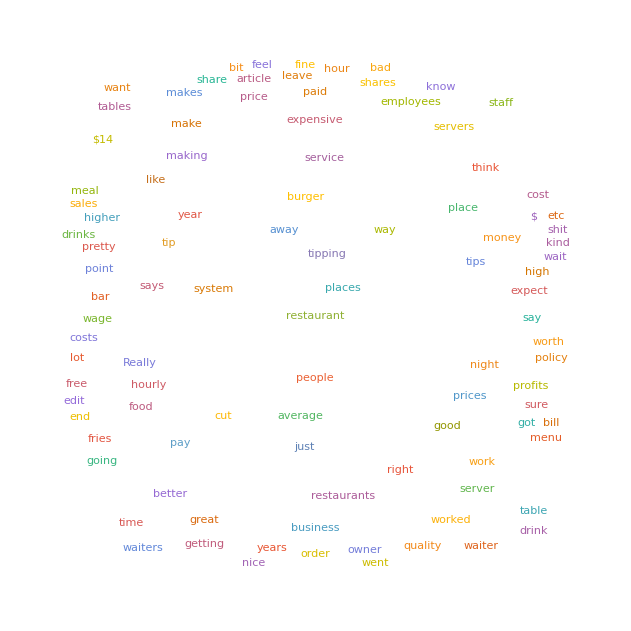

```mathematica
WordCloud[words]
```

```mathematica
wordFrequency=SortBy[Map[Rule@@#&,Tally[words]],Last]//Reverse;
```

```mathematica
Column[wordFrequency]
```

```mathematica
sentences=Flatten[Map[TextSentences,RandomSample[comments,All]]];
```

```mathematica
sentences[[2]]
```

I worked at a shoddy restaurant with insanely high quality steaks.

```mathematica
TextStructure[sentences[[2]]]
```

I
Pronoun
Noun Phrase  worked
Verb  at
Preposition  a
Determinershoddy
Adjectiverestaurant
Noun
Noun Phrase
Prepositional Phrase  with
Preposition    insanely
Adverbhigh
Adjective
Adjective Phrasequality
Nounsteaks
Noun
Noun Phrase
Prepositional Phrase
Verb Phrase.
Punctuation
Sentence

```mathematica
result=Flatten[Map[TextCases[#,"Adjective"]&,sentences]]
```

{stupid,worst,personal,better,ridiculous,frustrating,certain,additional,full,Seems,illegal,fancy,more,less,better,occasional,it's,financial,happily,weird,favorite,pupusas,reasonable,local,likely,unexpected,appalling,Good,native,weird,other,good,cheapest,cheapest,$20,total,single,$10,extra,double,real,different,Standard,good,least,upper,highest,minimum,developed,current,less,enthusiastic,decent,nice,good,i'm,attractive,first,psycho,bad,single,accomplished,prominent,more,good,important,powerful,enough,weird,colourful,you're,much,wait,great,shit,great,shit,much,motivated,much,bigger,hourly,worst,you're,fine,don't,old,sure,short,right,First,free,bottom,gravy,good,best,false,nice,new,last,meaningless,many,great,profitable,it's,profitable,good,successful,successful,first,real,fake,only,latter,disingenuous,theological,laughable,best,bitter,worst,other,fake,don't,regular,counterfeit,asshole,Last,tiny,old,first,few,other,other,personal,same,little,personal,Most,that's,male,old,many,visible,front,few,back,sole,invaluable,worth,more,long,overly,friendly,most,just,small,likely,efficient,general,uncommon,away,bigger,willing,constant,interesting,least,mid-to-upper,other,god,true,it's,low,hard,much,menu,complicated,it's,better,better,nice,nice,old,fondue,close,midweek,expensive,cheap,non-fast,little,high,expensive,expensive,good,major,important,plate,didn't,less,many,it's,small,sure,sure,safe,fancier,large,national,retail,advancement,initial,harder,unskilled,decent,same,silly,midwestern,few,sure,young,second,few,pricey,successful,large,enough,bad,more,standard,deli,Did,leave,worse,actual,guilty,same,expensive,average,more,odd,salaried,waiter's,net,last,bigger,busboys,net,great,$200,nights,bad,net,weekday,fine,net,normal,night-long,$18,weekday,punish,key,cashier's,concrete,expensive,more,more,better,next,right,non,last,shiny,ludicrous,same,double,high,good,high-scale,high,$14,reasonable,useless,good,good,good,hot,few,most,other,same,entire,owner's,near,complete,other,few,former,shoddy,high,friday,saturday,average,few,least,little,more,total,dive,nice,worse,cheese,nationwide,$9,much,high-end,great,permanent,great,great,company's,few,permanent,interesting,fucked,yr,minimum,wait,thier,due,super,decent,tip,unique,same,same,expensive,more,$4,enough,same,$25,able,more,wait,better,real,personal,low,nice,surprising,skilled,regular,few,free,strong,few,national,positive,curious,national,expensive,$9,expensive,major,cheap,average,expensive,own,nonsense,fake,fictional,retooled,cheaper,local,shareable,funny,great,only,higher,lean,tripled,free,early,prep,sure,good,darn,reasonable,lower,misleading,last,good,sure,first,many,lievable,biggest,tip,guilt,non,judgemental,major,fine,normal,high,most,crazy,it's,reasonable,good,fancy,$14,larger,first,same,different,little,own,tipping,custom,small,fancy,high,average,cheaper,high,Floridian,greater,good,great,true,particular,Weekly,low,hard,clear,professional,little,low,worth,most,everyone's,tip-based,same,different,uncommon,worse,better,single,bad,assigned,bad,bad,regular,sized,$14,normal,tiny,high,likely,worth,live,retooled,smaller,higher,higher,less,less,due,retooled,higher,open,tip-based,hourly,such,different,hourly,hourly,much,much,better,higher,worth,same,£9.13,that's,expensive,cheaper,overall,r,obnoxious,good,bad,same,dumb,variable,more,efficient,Second,slow,waiter's,slow,bad,good,total,real,we're,more,good,next,same,finest,high,over...they're,least,expensive,free,worth,less,double,normal,super,able,save,certain,fine,vast,more,it's,nice,cold,nasty,real,expensive,local,old,hard,more,sure,OK,only,good,that's,private,tough,better,best,obvious,better,sister](https://www.reddit.com/r/TwoXChromosomes/comments/3lb3nq/my_abusive_sisters_finally_been_evicted,needle,better,public,other,third,im,sure,it's,common,fast,depending,direct,full,equivalent,most,expensive,last,nice,casual,upper,bad,next,Most,full,high,Most,free,inattentive,long,Restaurant,helpful,non-tourist,different,many,run,it's,transparent,few,perverse,primary,remarkable,most,happy,backward,american,old,expensive,empty,10%,few,fine,guest's,common,mandatory,Rich,free,right,better,few,Good,more,high,happy,overall,happy,short,sure,great,overly,friendly,most,just,most,less,worthwhile,guilty,expensive,20%,higher,most,real,total,good,20%,free,low,$15,full,low,fancy,similar,experienced,nice,clear,more,hourly,hard,hourly,unfair,half,decent,easy,much,fast,cheap,typical,upscale,good,whole,expensive,major,metropolitan,sure,Rural,much,minimum,hourly,people's,several,several,best,typical,average,few,good,single,local,average,$51k,such,more,mindful,front,good,former,different,big,most,lazy,higher,only,due,negative,viable,worth,more,holy,surprised,first,likely,due,she'll,fancy,few,good,marginal,$10,most,least,£10.00,Large,important,other,huge,non,shit-per-hour,determine,adequate,fanciest,cheapest,able,good,primary,stable,higher,unreliable,Restaurant,bad,frivolous,other,steady,better,large,it's,$24,worth,run,weekly,allowable,free,new,regular,allowable,due,free,$8,flat,$30,more,less,same,single,consistent,much,true,tipped,customer's,bad,marginal,higher,american,new,free,aware,good,least,only,good,first,smaller,lower,original,first,great,expensive,unreasonable,expensive,general,special,last,good,pricey,good,attentive,multiple,sure,much,many,reliable,sick,that's,valuable,whole,huge,impossible,first,better,most}

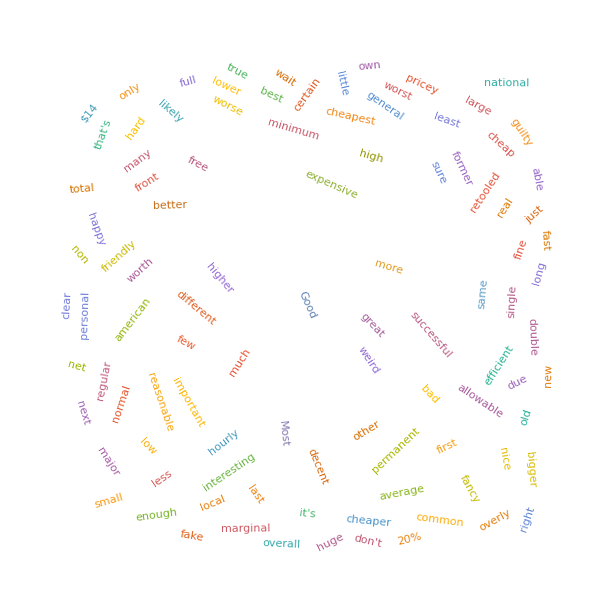

```mathematica
WordCloud[result,WordOrientation->"Random"]
```

```mathematica
Options[WordCloud]
```

{AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→GrayLevel[0, 0],BaselinePosition→Automatic,BaseStyle→{},ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,Epilog→{},FontFamily→Helvetica,FontSize→Automatic,FontTracking→Plain,FontWeight→Plain,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},IgnoreCase→True,ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxItems→Automatic,Method→Automatic,PlotLabel→None,PlotRange→Automatic,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→Identity,Ticks→Automatic,TicksStyle→{},WordOrientation→Horizontal,WordSpacings→Automatic,DisplayFunction:>$DisplayFunction,FormatType:>TraditionalForm}